## Линейное

#### Симметричный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Integro_interpolation_mult_0.500000.txt"]],Table[Real,n+1]];
(*k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]*)
```

```mathematica
(*Manipulate[ListContourPlot[TAll⟦i⟧],{i,1,k-1}]*)
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

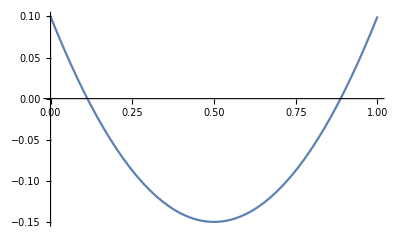

```mathematica
Plot[x^2-x+0.1,{x,0,1}]
```

#### Явный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Integro_interpolation_mult_0.000000.txt"]],Table[Real,n+1]];
(*k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]*)
```

ReadList::readn: Invalid real number found when reading from C:\Users\lenovo\source\repos\heat_conduction-\Integro_interpolation_mult_0.000000.txt.

```mathematica
(*Manipulate[ListContourPlot[TAll⟦i⟧],{i,1,k-1}]*)
```

```mathematica
ListPlot3D[plots,(* PlotRange->All,*) AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Неявный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Integro_interpolation_mult_1.000000.txt"]],Table[Real,n+1]];
(*k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]*)
```

```mathematica
ListPlot3D[plots,(* PlotRange->All,*) AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

## Точное решение (одна температура на концах, линейное K)

```mathematica
ClearAll["Global`*"]
```

```mathematica
c=1;ρ=1;u0 = 0.0;L=π;
k1 = 1;k2 = 0.1;
x1 = 1/3;x2 = 4/5;
```

```mathematica
K[x_]:=(* If[x ≤x1,k1,If[x1<x<x2,k1 (x-x2)/(x1-x2)+k2 (x-x1)/(x2-x1),k2]]*)1;
ut0[x_]:=(*u0-x(L-x)*)Sin[x];
```

```mathematica
sol = NDSolve[{c ρ D[u[t,x],t]==D[K[x]*D[u[t,x],x],x],u[0,x]==ut0[x],u[t,0]==u0,u[t,L]==u0},u,{t,0,1},{x,0,L}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
Plot3D[Evaluate[u[t,x]/.First[sol],{t,0,1},{x,0,L}],PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

## Квазилинейное

#### Прогонка

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Quasilinear.txt"]],Table[Real,n]];
(*k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]*)
```

```mathematica
(*Manipulate[ListContourPlot[TAll⟦i⟧],{i,1,k-1}]*)
```

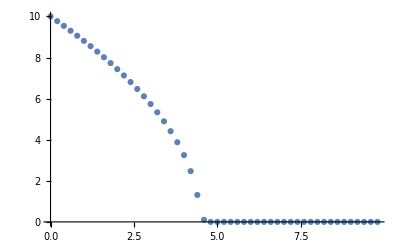

```mathematica
ListPlot[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

#### Нелинейное

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Non_linear.txt"]],Table[Real,n]];
(*k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]*)
```

```mathematica
(*Manipulate[ListContourPlot[TAll⟦i⟧],{i,1,k-1}]*)
```

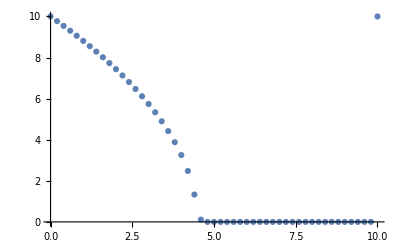

```mathematica
ListPlot[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

## Точное решение (одна температура на концах, нелинейное K)

```mathematica
ClearAll["Global`*"]
```

```mathematica
c=1;ρ=1;u0 = 0.0;L=10;T=2;
α = 0;β =0.5 ;γ =2;
```

```mathematica
K[x_]:= α+β x^γ;
ut0[x_]:=(*u0-x(L-x)*)10 √x;
```

```mathematica
sol = NDSolve[{c ρ D[u[t,x],t]==D[K[u[t,x]]*D[u[t,x],x],x],u[0,x]==u0,u[t,0]==ut0[t], K[u[t,L]]Derivative{0,1}[u][t,L]==0},u,{t,0,T},{x,0,L}]
```

NDSolve::dvnoarg: The function u appears with no arguments.

NDSolve[{u^(1,0)[t,x]==1. u[t,x] (u^(0,1)[t,x])^2+0.5 u[t,x]^2 u^(0,2)[t,x],u[0,x]==0.,u[t,0]==10 √t,0.5 Derivative u[t,10]^2 {0,1}[u][t,10]==0},u,{t,0,2},{x,0,10}]

```mathematica
Plot3D[Evaluate[u[t,x]/.First[sol],{t,0,T},{x,0,L}],PlotRange->All,ColorFunction->"Rainbow"]
```

ReplaceAll::reps: {u^(1,0)[t,x]==1. u[t,x] (u^(0,1)[t,x])^2+0.5 u[t,x]^2 u^(0,2)[t,x],u[0,x]==0.,u[t,0]==10 √t,0.5 Derivative u[t,10]^2 {0,1}[u][t,10]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {u^(1,0)[0.000143,0.000715]==1. u[0.000143,0.000715] (u^(0,1)[0.000143,0.000715])^2+0.5 u[0.000143,0.000715]^2 u^(0,2)[0.000143,0.000715],u[0,0.000715]==0.,«1»,0.5 Derivative u[«23»,10]^2 {0,1}[u][0.000143,10]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {u^(1,0)[0.000143,0.000715]==1. u[0.000143,0.000715] (u^(0,1)[0.000143,0.000715])^2+0.5 u[0.000143,0.000715]^2 u^(0,2)[0.000143,0.000715],u[0.,«9»]==«3»,«1»,0.5 Derivative u[«23»,«4»]^2 {0.,1.}[u][0.000143,10.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics3D-

## Квазилинейное из методички

```mathematica
Clear["Global`*"]
```

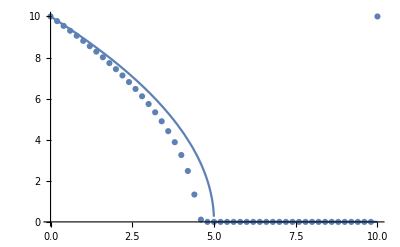

```mathematica
σ = 2;κ = 0.5;c = 5;T = 1;L=10;
u0 = ((σ c^2)/κ)^(1/σ);
u[x_,t_]:=If[xc t,(σ c κ^-1(c t - x))^(1/σ),0];
t=1;
Show[Plot[Evaluate[u[x,t],{x,0,L}],PlotRange->All], ListPlot[plots, PlotRange->All, AxesLabel->Automatic]]
```